```mathematica
GeoCanberraDistance[pointA_]:=CanberraDistance[First[GeoPositionXYZ[pointA]],First[GeoPositionXYZ[Here]]]
GeoCanberraDistance[pointA_,pointB_]:=CanberraDistance[First[GeoPositionXYZ[pointA]],First[GeoPositionXYZ[pointB]]]
```

```mathematica
GeoCanberraDistance[GeoAntipode[Here]]
```

3.

```mathematica
GeoCanberraDistance[GeoPosition["NullIsland"]]
```

2.81287

```mathematica
Rationalize[GeoCanberraDistance[GeoPosition["NullIsland"]]]
```

2.81287

```mathematica
GeoPositionXYZ[Here]
```

GeoPositionXYZ[{658385.,-4.96078×10^6,3.94121×10^6}]

```mathematica
Round/@First[GeoPositionXYZ[Here]]
```

{658385,-4960783,3941206}

```mathematica
CanberraDistance[{a,b,c},{x,y,z}]
```

Abs[a-x]/(Abs[a]+Abs[x])+Abs[b-y]/(Abs[b]+Abs[y])+Abs[c-z]/(Abs[c]+Abs[z])

```mathematica
CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{x,y,z}]
```

Abs[658385-x]/(658385+Abs[x])+Abs[-4960783-y]/(4960783+Abs[y])+Abs[3941206-z]/(3941206+Abs[z])

```mathematica
CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{0,0,0}]
```

3

```mathematica
CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{0,0,1}]
```

11823619/3941207

```mathematica
3-CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{0,0,1}]
```

2/3941207

```mathematica
RandomReal[5,100]
```

{1.28368,3.99687,1.78313,0.117817,0.0662024,0.986593,0.612317,4.43726,3.40001,1.66111,3.97343,0.429348,2.88084,0.85629,2.26339,4.34128,2.54121,2.52675,4.28217,1.4547,0.569382,2.13403,0.319806,0.4323,4.05274,2.96401,1.42008,4.48242,4.85335,4.21793,0.784299,4.87891,2.96802,2.82574,0.889207,1.03055,3.45015,3.39243,1.06734,1.61043,2.39065,2.27428,2.90396,2.1885,2.20554,3.06767,4.58304,2.01941,0.635132,0.297455,4.91299,3.29391,3.17621,3.44589,2.93124,0.870477,2.66643,1.20251,1.10805,0.514491,1.01326,3.32528,4.37625,0.145945,4.16618,0.847435,3.8509,0.79768,0.371528,3.32955,0.644631,1.88911,0.0114881,4.89297,3.11801,1.0681,4.30748,2.64235,0.103202,0.674787,4.84591,2.05491,2.59463,0.489163,2.86145,3.36957,4.11479,4.44592,4.97545,3.78146,0.294127,2.48138,4.15597,0.0409825,0.800541,4.94351,3.17195,4.5259,3.07415,4.15561}

```mathematica
CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{0,0,1}]
```

```mathematica
Round/@First[GeoPositionXYZ[GeoAntipode@Here]]
```

{-658385,4960783,-3941206}

```mathematica
CanberraDistance[Round/@First[GeoPositionXYZ[Here]],Round/@First[GeoPositionXYZ[GeoAntipode@Here]]]
```

3

```mathematica
CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{0,0,z}]
```

2+Abs[3941206-z]/(3941206+Abs[z])

```mathematica
FunctionRange[2+Abs[3941206-z]/(3941206+Abs[z]),z,g]
```

2≤g≤3

```mathematica
ManhattanDistance[Round/@First[GeoPositionXYZ[Here]],{0,0,z}]
```

5619168+Abs[3941206-z]

```mathematica
ManhattanDistance[Round/@First[GeoPositionXYZ[Here]],{0,0,1}]
```

9560373

```mathematica
CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{0,0,1}]
```

11823619/3941207

```mathematica
3-CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{0,0,1}]
```

2/3941207

```mathematica
ManhattanDistance[Round/@First[GeoPositionXYZ[Here]],{0,0,1}]
```

9560373

```mathematica
2/ManhattanDistance[Round/@First[GeoPositionXYZ[Here]],{0,0,1}]
```

2/9560373

```mathematica
FunctionRange[Abs[3941206-z]/(3941206+Abs[z]),z,g]
```

0≤g≤1

```mathematica
CanberraDistance[{x},{1}]
```

Abs[-1+x]/(1+Abs[x])

```mathematica
FunctionRange[CanberraDistance[{x},{1}],x,y]
```

0≤y≤1

```mathematica
FunctionDomain[CanberraDistance[{x},{1}],x]
```

True

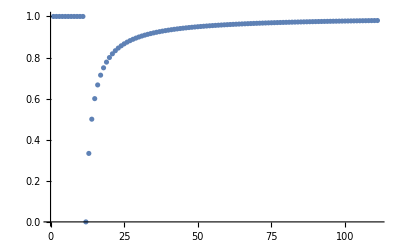

```mathematica
ListPlot[CanberraDistance[{#},{1}]&/@Range[-10,100]]
```

```mathematica
CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{10000,100,1}]
```

1564781089063/526848728139

```mathematica
N[1564781089063/526848728139,100]
```

2.970076618748445284267567037737648636316849643322965182480440267163782167970298826748099243929491285

```mathematica
N[1564781089063/526848728139,100]
```

2.970076618748445284267567037737648636316849643322965182480440267163782167970298826748099243929491285

```mathematica
N[1564781089063/526848728139,100]-N[1564781089063/526848728139,100]
```

0.

```mathematica
CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{10000,100,1}]==CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{10000,1000,1}]
```

True

```mathematica
CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{10000,100,1}]===CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{10000,1000,1}]
```

True

```mathematica
CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{10000,10,1}]===CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{10000,100,1}]
```

True

```mathematica
CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{10000,1,1}]===CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{10000,10,1}]
```

True

```mathematica
CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{10000,1,1}]===CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{10000,1,1}]
```

True

```mathematica
CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{10000,0,1}]===CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{10000,1,1}]
```

True

```mathematica
CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{1000,0,1}]===CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{10000,1,1}]
```

False

```mathematica
CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{1000,0,1}]
```

1557686920063/519754555539

```mathematica
CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{10000,1,1}]
```

1564781089063/526848728139

```mathematica
CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{10001,1,1}]
```

3911954693260/1317123790951

```mathematica
N[CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{10001,1,1}],20]
```

2.9700736712343947099

```mathematica
N[CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{10002,1,1}],20]
```

2.9700707237291639182

```mathematica
N[CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{10002,1,1}],20]<N[CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{10001,1,1}],20]
```

True

```mathematica
N[CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{-10002,1,1}],20]<N[CanberraDistance[Round/@First[GeoPositionXYZ[Here]],{10001,1,1}],20]
```

False

```mathematica
GeoCanberraDistance[GeoAntipode[Here]]
```

3.

```mathematica
FullForm[GeoCanberraDistance[GeoAntipode[Here]]]
```

3.

```mathematica
NumberForm[3.,16]
```

3.

```mathematica
FullForm[GeoCanberraDistance[GeoAntipode[Here]]]
```

```mathematica
Round/@First[GeoPositionXYZ[Here]]
```

{658385,-4960783,3941206}

```mathematica
Round/@First[GeoPositionXYZ[GeoPosition["NorthModelDipPole"]]]
```

{-361814,223104,6342620}

```mathematica
CanberraDistance[{a,b,c},{x,y,z}]
```

Abs[a-x]/(Abs[a]+Abs[x])+Abs[b-y]/(Abs[b]+Abs[y])+Abs[c-z]/(Abs[c]+Abs[z])

```mathematica
CanberraDistance[{a,b,c},{x,y,z}]/.{a->658385,b->-4960783,c->3941206,x->-361814,y->223104,z->6342620}
```

11484533/5141913

```mathematica
N[CanberraDistance[{a,b,c},{x,y,z}]/.{a->658385,b->-4960783,c->3941206,x->-361814,y->223104,z->6342620},10]
```

2.233513675

```mathematica
N[CanberraDistance[{a,b,c},{x,y,z}]/.{a->658385,b->-4960783,c->3941206,x->-361814,y->0,z->6342620},10]
```

2.233513675

```mathematica
N[CanberraDistance[{a,b,c},{x,y,z}]/.{a->658385,b->-4960783,c->3941206,x->658385,y->-4960783,z->6342620},10]
```

0.2335136748

```mathematica
N[CanberraDistance[{a,b,c},{x,y,z}]/.{a->658385,b->-4960783,c->3941206,x->658385,y->-4960783,z->3941206},10]
```

0

```mathematica
N[CanberraDistance[{a,b,c},{x,y,z}]/.{a->658385,b->-4960783,c->3941206,x->-658385,y->-4960783,z->3941206},10]
```

1.

```mathematica
N[CanberraDistance[{a,b,c},{x,y,z}]/.{a->658385,b->-4960783,c->3941206,x->-658385,y->4960783,z->3941206},10]
```

2.

```mathematica
N[CanberraDistance[{a,b,c},{x,y,z}]/.{a->658385,b->-4960783,c->3941206,x->-658385,y->4960783,z->-3941206},10]
```

3.

```mathematica
N[CanberraDistance[{a,b,c},{x,y,z}]/.{a->658385,b->-4960783,c->3941206,x->-658385,y->7960783,z->-3941200}]
```

3.

```mathematica
N[CanberraDistance[{a,b,c},{x,y,z}]/.{a->658385,b->-4960783,c->3941206,x->-658385,y->7960783,z->-3941200},10]
```

3.

```mathematica
N[CanberraDistance[{a,b,c},{x,y,z}]/.{a->658385,b->-4960783,c->3941206,x->-658385,y->7960783,z->-3941200},1000]
```

3.

```mathematica
CanberraDistance[{0},{0}]
```

0

```mathematica
CanberraDistance[{0},{1}]
```

1

```mathematica
CanberraDistance[{1},{1}]
```

0

```mathematica
CanberraDistance[{1},{2}]
```

1/3

```mathematica
{#,CanberraDistance[{#},{#+1}]}&/@Range[10]
```

{{1,1/3},{2,1/5},{3,1/7},{4,1/9},{5,1/11},{6,1/13},{7,1/15},{8,1/17},{9,1/19},{10,1/21}}

## Testing CanberraDistance

```mathematica
GeoCanberraDistance[GeoAntipode[Here]]
```

3.

```mathematica
GeoCanberraDistance[GeoAntipode["NullIsland"],GeoPosition["NullIsland"]]
```

2.

```mathematica
GeoCanberraDistance[GeoPosition["NorthPole"]]
```

2.23457

```mathematica
GeoCanberraDistance[GeoPosition["SouthPole"]]
```

3.

```mathematica
GeoCanberraDistance[GeoPosition["NorthGeomagneticPole"]]
```

1.26035

```mathematica
GeoCanberraDistance[GeoPosition["SouthGeomagneticPole"]]
```

3.

```mathematica
GeoCanberraDistance[GeoPosition["SouthModelDipPole"]]
```

3.

```mathematica
GeoCanberraDistance[GeoPosition["NorthModelDipPole"]]
```

2.23351

```mathematica
NumberForm[2.233513664209488,16]
```

2.233513664209488

```mathematica
CanberraDistance[{1,1,1},{2,2,2}]
```

1

```mathematica
CanberraDistance[{1,1,1},{4,4,4}]
```

9/5

```mathematica
CanberraDistance[{1,1,1},{4,4,4}]
```

9/5

```mathematica
Abs[{1,1,1}]
```

{1,1,1}

```mathematica
Abs[{4,4,4}]
```

{4,4,4}

```mathematica
Abs[{1,1,1}-{4,4,4}]
```

{3,3,3}

```mathematica
Abs[{1,1,1}-{4,4,4}]/(Abs[{1,1,1}]+Abs[{4,4,4}])
```

{3/5,3/5,3/5}

```mathematica
Total[Abs[{1,1,1}-{4,4,4}]/(Abs[{1,1,1}]+Abs[{4,4,4}])]
```

9/5

```mathematica
Abs[{1,1,1}-{4,4,40}]/(Abs[{1,1,1}]+Abs[{4,4,40}])
```

{3/5,3/5,39/41}

```mathematica
N[Abs[{1,1,1}-{4,4,40}]/(Abs[{1,1,1}]+Abs[{4,4,40}])]
```

{0.6,0.6,0.95122}